```mathematica
V0=25
```

25

```mathematica
L=1
```

1

```mathematica
V[x_]:=-V0/2*(1+Cos[2*Pi*x/L])/;Abs[x]<=L/2
V[x_]:=0 /; Abs[x]>L/2
```

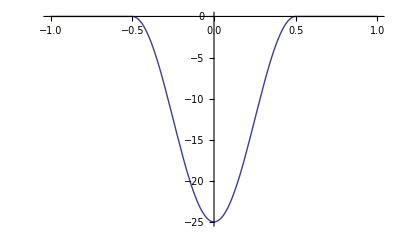

```mathematica
Plot[V[x],{x,-L,L}]
```

```mathematica
B = 1;
```

```mathematica
ψ1[x_] := A Exp[ Abs[2 en]^(1/2) x]
ψ3[x_] := B Exp[- Abs[2 en]^(1/2) x]
```

```mathematica
eqn[en_] := ψ2''[x] + 2(en - V[x])ψ2[x]
```

```mathematica
wavefunc2[energy_] :=(
en = energy; 
NDSolve[
{ eqn[energy] == 0, ψ2[-L/2] ==  ψ1[-L/2], ψ2'[-L/2] ==  ψ1'[-L/2]}, 
ψ2, 
{x, -L/2, 0} 
]
)
```

```mathematica
sol2[x_?NumericQ, en_?NumericQ] := ψ2[x] /. wavefunc2[en][[1]]
```

```mathematica
sol2prime[x_?NumericQ,en_?NumericQ]:=ψ2'[x]/.wavefunc2[en][[1]]
```

```mathematica
A = B;
```

```mathematica
eval = energy /. FindRoot [ sol2prime[0, energy],{energy, -5, -8} ]
```

-15.329

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2 ;
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0;
ψnn[x_] := ψ1[x] /; x < -L/2 ;
ψnn [x_] := ψ3[x] /; x > L/2;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

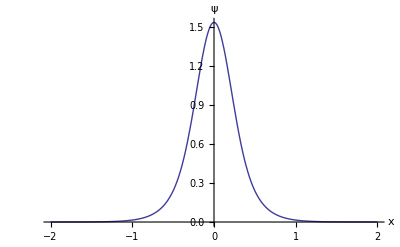

```mathematica
Plot[ψ[x], 
{x, -2.0L, 2.0L}, 
AxesLabel -> {"x", "ψ"} ]
```

```mathematica
A = -B;
```

```mathematica
eval = en /. FindRoot [sol2[0, en] ,{en, -0.5, -2.0} ]
```

-21.6391

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0;
ψnn [x_] := -efunc2[-x] /; 0 ≤  x  ≤  L/2 ;
ψnn[x_] := ψ1[x] /; x < -L/2 ;
ψnn [x_] := ψ3[x] /; x > L/2;
```

```mathematica
normconst = Sqrt[NIntegrate [ ψnn[x]^2, {x, -Infinity,Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

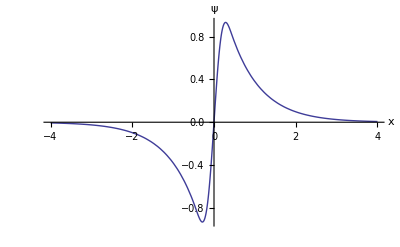

```mathematica
Plot[ψ[x], 
{x, -4L,4L},
AxesLabel -> {"x", "ψ"} 
]
```

```mathematica
V0=70
```

70

```mathematica
V[x_]:=-V0/2*(1+Cos[2*Pi*x/L])/;Abs[x]<=L/2
V[x_]:=0 /; Abs[x]>L/2
```

```mathematica
A = B;
```

```mathematica
BB={}
```

{}

```mathematica
Do[BB=DeleteDuplicates[Append[BB,en /. FindRoot [sol2prime[0, en] ,{en, -i, -i-1} ]]], {i,1,100}]
```

```mathematica
BB
```

{-0.966301,-0.966301,-0.966301,-0.966301,-0.966301,174.306,66.9109,66.9109,66.9109,66.9109,174.306,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753,-52.753}

```mathematica
BB={-0.9663011693997166,-52.75296519370829,66.91086684769668,174.30614207744432}
```

{-0.966301,-52.753,66.9109,174.306}

```mathematica
eval=BB[[1]]
```

-0.966301

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2 ;
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0;
ψnn[x_] := ψ1[x] /; x < -L/2 ;
ψnn [x_] := ψ3[x] /; x > L/2;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

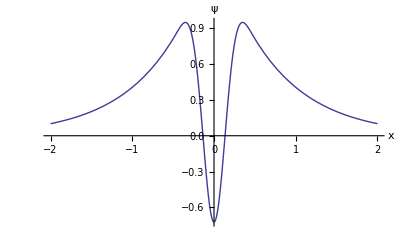

```mathematica
Plot[ψ[x], 
{x, -2.0L, 2.0L}, 
AxesLabel -> {"x", "ψ"} ]
```

```mathematica
eval=BB[[2]]
```

-52.753

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2 ;
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0;
ψnn[x_] := ψ1[x] /; x < -L/2 ;
ψnn [x_] := ψ3[x] /; x > L/2;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

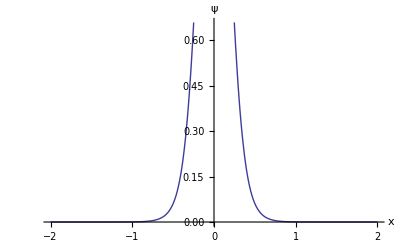

```mathematica
Plot[ψ[x], 
{x, -2.0L, 2.0L}, 
AxesLabel -> {"x", "ψ"} ]
```

```mathematica
eval=BB[[3]]
```

66.9109

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2 ;
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0;
ψnn[x_] := ψ1[x] /; x < -L/2 ;
ψnn [x_] := ψ3[x] /; x > L/2;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

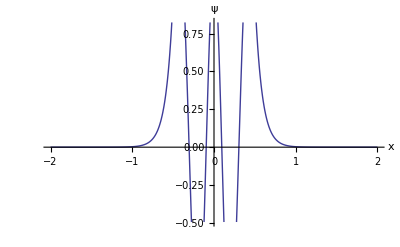

```mathematica
Plot[ψ[x], 
{x, -2.0L, 2.0L}, 
AxesLabel -> {"x", "ψ"} ]
```

```mathematica
eval=BB[[4]]
```

174.306

```mathematica
efunc2[x_]=ψ2[x]/.wavefunc2[eval][[1]];
```

```mathematica
ψnn [x_] := efunc2[-x] /; 0 ≤  x  ≤  L/2 ;
ψnn[x_] := efunc2[x] /; -L/2 ≤  x  < 0;
ψnn[x_] := ψ1[x] /; x < -L/2 ;
ψnn [x_] := ψ3[x] /; x > L/2;
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -Infinity, Infinity} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

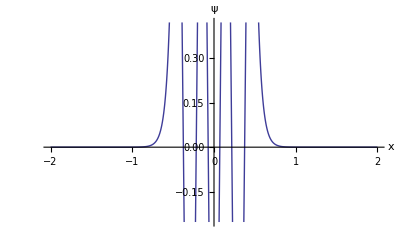

```mathematica
Plot[ψ[x], 
{x, -2.0L, 2.0L}, 
AxesLabel -> {"x", "ψ"} ]
```